```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY196/sec_int_data/412nm.dat"]
```

{{1.64105,-0.146449},{1.57964,-0.143039},{1.51907,-0.0757586},{1.47433,-0.070519},{1.70936,-0.151509},{1.78557,-0.166964}}

0.390226-0.318837 x

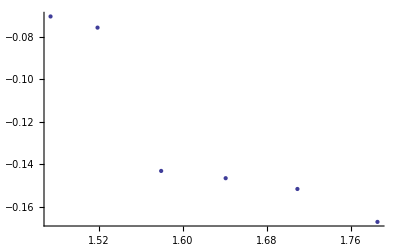

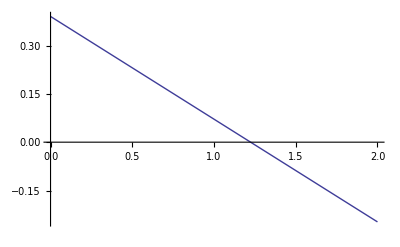

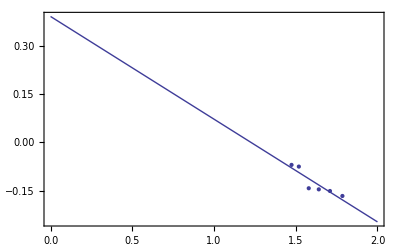

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```